#### (Quit the Kernel then run the cells) Phase and Time-Plots of the different regions of the two-parameter bifurcation map illustrated in the paper “Dynamics of a SIR epidemic model with limited medical resources, revisited again”(EcoEvo)

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];<<"def.m";
(*Contains dis, trE2,BP,BTP*)
R0=(β Λ)/(μ (γ+δ+η+μ));
cp={Λ>0,δ>0,γ>0,β>0,ξ>0,ω>0,μ>0,α>0,η>0};

<<EcoEvo`
(*EcoEvoDocs;*)
ClearParameters;UnsetModel; 
SetModel[{Pop[s]->{Equation:>(-(i s β)/(1+i ξ)+Λ-s μ),Color->Green},Pop[i]->{Equation:>(-(i α)/(i+ω)+(i s β)/(1+i ξ)-i (γ+δ+μ)),Color->Blue},
 Parameters:>cp}]
(*Very long symbolic fixed points*)
equi=SolveEcoEq[];
```

EcoEvo Package Version 1.6.4 (November 5, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

#### Phase plot of the region I:

TrE2=

0.0132728

Fixed points:{{s→133.3333333333333333,i→0},{s→86.1360539071632346,i→6.61878494502023444},{s→69.95888114064486073,i→10.99004545382992726}}

Eigenvalues of FP:{{-24.6780952380952381,-0.12},{0.284436318392349985,-0.0668762268402831884},{0.00663638043549540564+0.137909388977886219 ⅈ,0.00663638043549540564-0.137909388977886219 ⅈ}}

Time plot around E2

{s→70.0389,i→11.}

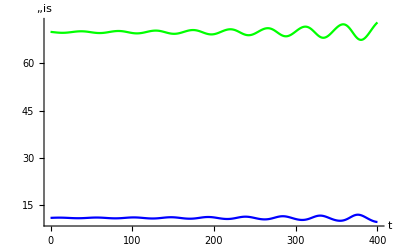

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

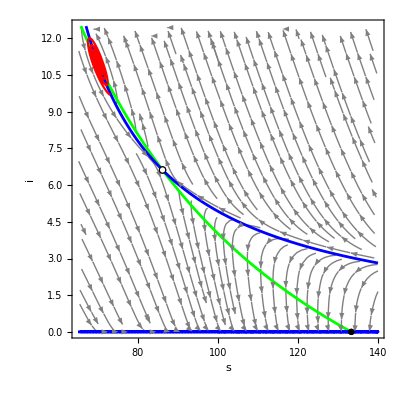

Final time slice is

0.205297

The floquet exponents are

{-0.12,-24.6781}

spRIE.pdf

solTI.pdf

```mathematica
ClearParameters;
T=400;
xM=140;
xm=65;
yM=12.5;
ym=0;
Λ=16 ;δ=1/5;γ=3/25;β=1/100;ξ=1/1000;μ=3/25;
ω=7/64;α=179/64;η=α/ω;
Print["TrE2="]
trE2//N
eq=N[equi,19];
Print["Fixed points:",eq]

Print["Eigenvalues of FP:",EcoEigenvalues[eq]]

pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
E2n=RuleListTweak[eq[[3]],{s,i},{0.08,0.01}]
sol=EcoSim[E2n,T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spRIE.pdf",sp]

Export["solTI.pdf",psol]
```

#### Phase plot of the region II:

```mathematica
ClearParameters;
T=600;
xM=140;
xm=50;
yM=20;
ym=0;

RII=FindInstance[Join[{dis>0,R0>1,(trE2)>0},cp,{η==α/ω}]//.cut,{ω,α,η}]
(*Λ=16 ;δ=1/5;γ=3/25;β=1/100;xi=1/1000;μ=3/25;w=51/8 ;α=43/8;*)
cII=Flatten[Join[cut,RII]]
Print["Fixed points:"]
eq=equi/.cII//N
Print["Eigenvalues of FP:"]
EcoEigenvalues[eq]/.cII//N
eqs={s->IntegerPart[eq[[3,1]][[2]]],i->IntegerPart[eq[[3,2]][[2]]]}
```

{{ω→51/8,α→43/8,η→43/51}}

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→51/8,α→43/8,η→43/51}

Fixed points:

{{s→133.333,i→0.},{s→149.218,i→-1.27578},{s→85.4965,i→6.75961}}

Eigenvalues of FP:

{{-0.12,0.0501961},{-0.3429,-0.0261396},{0.00887972-0.13495 ⅈ,0.00887972+0.13495 ⅈ}}

{s→85,i→6}

{s→InterpolatingFunction[…],i→InterpolatingFunction[…]}

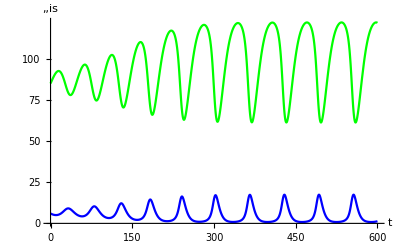

```mathematica
Λ=16 ;δ=1/5;γ=3/25;β=1/100;ξ=1/1000;μ=3/25;ω=51/8 ;α=43/8;
sol=EcoSim[eqs,T]
psol=PlotDynamics[sol]
```

Time plot around E2

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

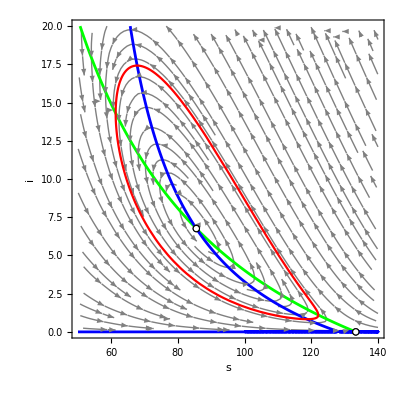

Final time slice is

63.5035

The floquet exponents are

{-3.20788×10^-8,-0.0228667}

spR2E.pdf

solT2.pdf

```mathematica
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]

Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[lc,{s,i},PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spR2E.pdf",sp]

Export["solT2.pdf",psol]
```

#### Phase plot of the region III:

Fixed points:

{{s→133.333,i→0.},{s→45.58,i→23.6495}}

Eigenvalues of FP:

{{0.867292,-0.12},{-0.178557+0.265984 ⅈ,-0.178557-0.265984 ⅈ}}

Time plot around E2

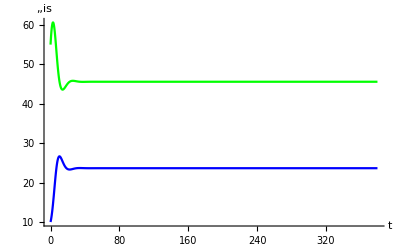

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

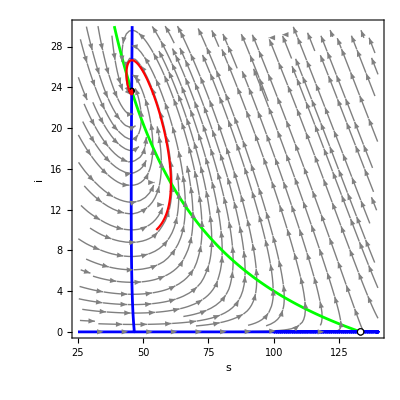

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spR3E.pdf

solT3.pdf

```mathematica
ClearParameters;
T=380;
xM=140;
xm=25;
yM=30;
ym=0;
Λ=16 ;δ=1/5;γ=3/25;β=1/100;ξ=1/1000;μ=3/25;
ω=6 ;α=5/32;
Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
EcoEigenvalues[eq]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->55,i->10},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spR3E.pdf",sp]

Export["solT3.pdf",psol]
```

#### Phase plot of the region IV:

TrE2=

-0.534435

Fixed points:{{s→133.3333333333333333,i→0},{s→3594.562322769512524,i→-11.42289302686083784},{s→177.102470355192846,i→-2.956912937925364096}}

Eigenvalues of FP:{{-0.12,-0.10666666666666667},{-1253.9784082524383,-0.0010619305903962781},{-0.557250711059899373,0.022816185444697038}}

Time plot around E2

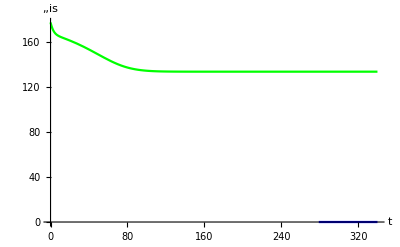

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

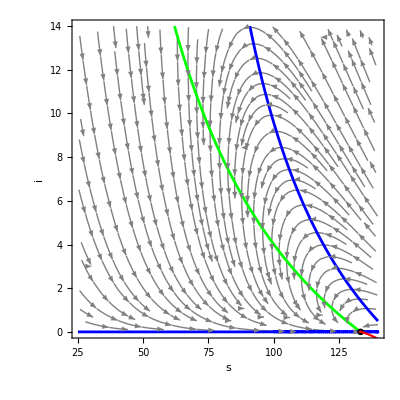

Final time slice is

1000.

The floquet exponents are

{-∞,-∞}

spRIVE.pdf

solTIV.pdf

```mathematica
ClearParameters;
T=340;
xM=140;
xm=25;
yM=14;
ym=0;
Λ=16 ;δ=1/5;γ=3/25;β=1/100;ξ=1/1000;μ=3/25;
ω=47/4;α=47/4;η=α/ω;
Print["TrE2="]
trE2//N
eq=N[equi,19];
Print["Fixed points:",eq]

Print["Eigenvalues of FP:",EcoEigenvalues[eq]]

pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[3,1]][[2]]],i->IntegerPart[eq[[3,2]][[2]]]+1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spRIVE.pdf",sp]

Export["solTIV.pdf",psol]
```

#### Phase plot of Region VIa :

7.49254

6.70396

Fixed points:{{s→133.3333333333333333,i→0},{s→130.4528532406476235,i→0.2650376858970212231},{s→122.3268071810354282,i→1.080883889607936805}}

Eigenvalues of FP:{{-0.12,-0.001418762507735599},{-0.094779579177624718,0.0013091616317688633},{-0.016766725157969118+0.013280939572437233 ⅈ,-0.016766725157969118-0.013280939572437233 ⅈ}}

We will evaluate near the point

Time plot around E2

{s→122.827,i→1.58088}

{s→130.463,i→0.285038}

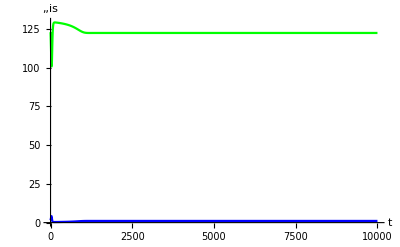

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

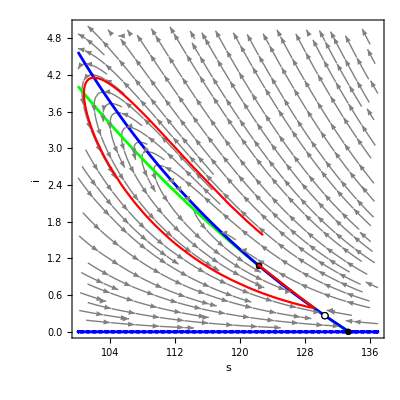

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spVIa.pdf

solVIa.pdf

```mathematica
ClearParameters;
T=10^4;
xM=137;
xm=100;
yM=5;
ym=0;
ω=502/67;α=41102/6131;Λ=16 ;δ=1/5;γ=3/25;β=1/100;ξ=1/1000;μ=3/25;
502/67//N
α//N
eq=N[equi,19];
Print["Fixed points:",eq]

Print["Eigenvalues of FP:",EcoEigenvalues[eq]]

pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["We will evaluate near the point "]

Print["Time plot around E2"]
E2n=RuleListTweak[eq[[3]],{s,i},{0.5,0.5}]
sol=EcoSim[E2n,T];
E1n=RuleListTweak[eq[[2]],{s,i},{0.01,0.02}]
sol1=EcoSim[E1n,T];
psol2=PlotDynamics[sol,PlotPoints->400];
psol1=PlotDynamics[sol1,PlotPoints->400,PlotStyle->{Yellow,Pink}];
psol=Show[psol2]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp2=Show[pp,RuleListPlot[sol,PlotStyle->Red,PlotPoints->400]];
sp1=Show[pp,RuleListPlot[sol1,PlotStyle->Magenta,PlotPoints->400]];
Show[sp2]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spVIa.pdf",sp2]
Export["solVIa.pdf",psol]
```

#### Phase plot of the boundary TrE2=0 between Regions I and VIa:

2.93233

3.69658

Fixed points:

{{s→133.3,i→0},{s→106.9,i→2.971},{s→73.82,i→9.77}}

Eigenvalues of FP:

{{-0.367,-0.12},{0.229,-0.0664},{0.152 ⅈ,-0.152 ⅈ}}

Time plot around E2

{i→9.77,s→74.6151}

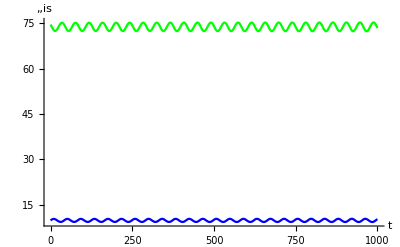

Finding the cycle using time slice

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

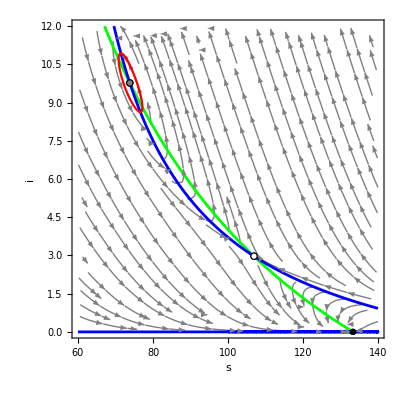

Final time slice is

41.7589

The floquet exponents are

{0.00149016,0.000030097}

sp16a.pdf

solT16a.pdf

```mathematica
ClearParameters;
T=10^3;
xM=140;
xm=60;
yM=12;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=390/133;α=Root"3.70"Root[-1631032149588767858556+1037597467095537232220 #1-172403183107836347975 #1^2+2995459825981969500 #1^3&,2]3.696581372014427;
(*251/71;α=Root"3.93"Root[-139002992484639814900593+78478625880764526752550 #1-11766747132421728060625 #1^2+202603249788006375000 #1^3&,2]3.9255178935033967;*)
ω//N
α//N

Print["Fixed points:"]
eq=N[equi,4]
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-12]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
E2n=RuleListTweak[eq[[3]],{s},{0.8}]
sol=EcoSim[E2n,T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[lc,{s,i},PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["sp16a.pdf",sp]
Export["solT16a.pdf",psol]
```

#### Phase plot of the boundary TrE2=0 between Regions II and III:

Fixed points:

{{s→133.3333333333333333,i→0},{s→148.254027835717964,i→-1.206256305190749303},{s→80.64038208876516802,i→7.903145785444163751}}

Eigenvalues of FP:

{{-0.12,0.058957665969571868},{-0.3387495211596356,-0.0301670848201448014},{0.151250071483287974 ⅈ,-0.151250071483287974 ⅈ}}

Time plot around E2

{s→80.64038208876516802,i→8.40315}

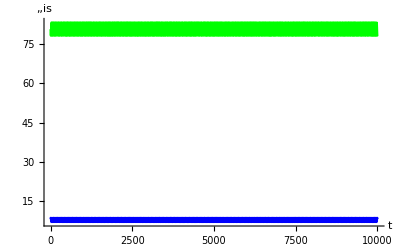

Finding the cycle using time slice

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

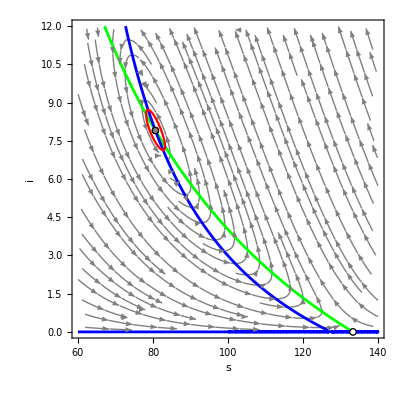

Final time slice is

41.6159

The floquet exponents are

{-3.18843×10^-7+0.0000102417 ⅈ,-3.18843×10^-7-0.0000102417 ⅈ}

spB23E.pdf

solT23.pdf

```mathematica
ClearParameters;
T=10^4;
xM=140;
xm=60;
yM=12;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=6 ;α=(*Rationalize[5.00625]*)Root[{-686757738052533+1647448543030550*#1-1077591212548125*#1^2+107367096375000*#1^3&,6*#1-#2&},{1,1}];

Print["Fixed points:"]
eq=N[equi,19]
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-12]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
E2n=RuleListTweak[eq[[3]],i,0.5]
sol=EcoSim[E2n,T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[lc,{s,i},PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB23E.pdf",sp]
Export["solT23.pdf",psol]
```

Fixed points:

{{s→133.333,i→0.},{s→80.6404,i→7.90315}}

Eigenvalues of FP:

{{-0.12,0.0589577},{0.+0.15125 ⅈ,0.-0.15125 ⅈ}}

Time plot around E2

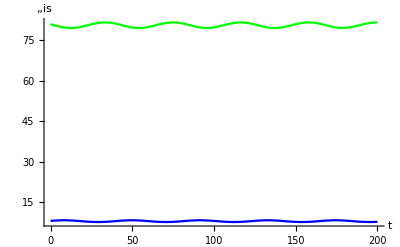

Finding the cycle using time slice

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

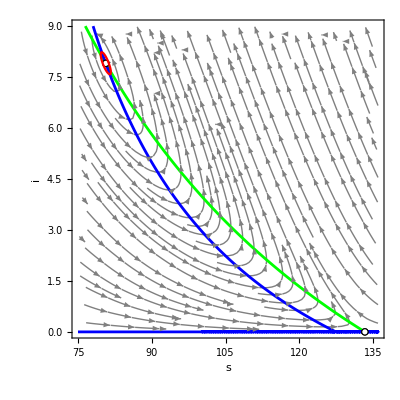

Final time slice is

41.5543

The floquet exponents are

{7.65401×10^-6,-7.57769×10^-6}

spB23Eb.pdf

solT23b.pdf

```mathematica
ClearParameters;
T=200;
xM=136;
xm=75;
yM=9;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=6 ;α=(*Rationalize[5.00625]*)Root[{-686757738052533+1647448543030550*#1-1077591212548125*#1^2+107367096375000*#1^3&,6*#1-#2&},{1,1}];

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-12]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]]+1,i->IntegerPart[eq[[2,2]][[2]]]+1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[lc,{s,i},PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB23Eb.pdf",sp]
Export["solT23b.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions VI and III ( between 0 and B1):

Fixed points:{{s→133.3333333333333333,i→0},{s→133.3333333333333333,i→0},{s→72.81753885193378788,i→10.07318548820525105}}

Eigenvalues of FP:{{-0.12,0},{-0.12,0},{-0.017169015179450851+0.173631522140559829 ⅈ,-0.017169015179450851-0.173631522140559829 ⅈ}}

Time plot around E2

{s→72.8275,i→10.8732}

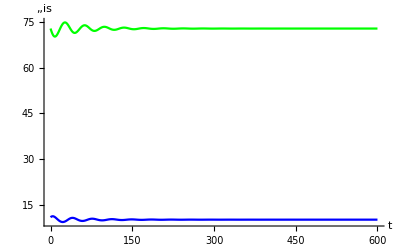

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

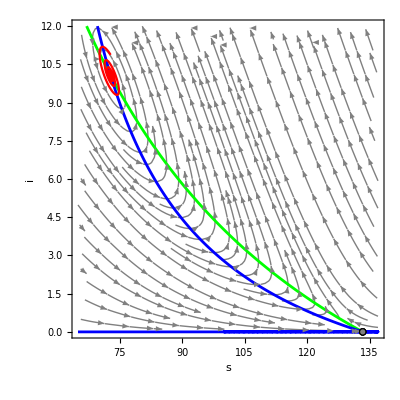

Final time slice is

40.607

sp0B1.pdf

sol0B1.pdf

```mathematica
ClearParameters;
T=600;
xM=137;
xm=65;
yM=12;
ym=0;
Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;
ω=901/195;
α=60367/14625;
eq=N[equi,19];
Print["Fixed points:",eq]

Print["Eigenvalues of FP:",EcoEigenvalues[eq]]

pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
E2n=RuleListTweak[eq[[3]],{s,i},{0.01,0.8}]
sol=EcoSim[E2n,T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
(*Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]*)
Export["sp0B1.pdf",sp]
Export["sol0B1.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions III and VI (Between BT and B1):

5.27737

4.71445

Fixed points:

{{s→133.333,i→0.},{s→79.9285,i→8.0827},{s→133.333,i→1.55832×10^-15}}

Eigenvalues of FP:

{{-0.12,0},{0.00347509+0.146926 ⅈ,0.00347509-0.146926 ⅈ},{-0.12,0}}

Time plot around E2

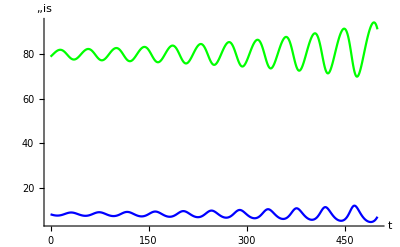

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

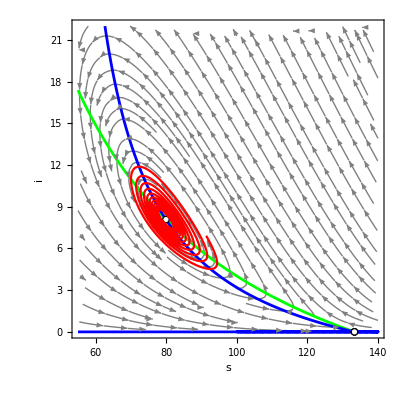

Final time slice is

101.348

The floquet exponents are

{8.51007×10^-8,-0.0337781}

spB12aE.pdf

solT12a.pdf

```mathematica
ClearParameters;
T=500;
xM=140;
xm=55;
yM=22;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=723/137//N 
α=16147/3425//N
(*ω=5.157354044656745;α=4.607236279893359;*)

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB12aE.pdf",sp]
Export["solT12a.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions III and VI (Between BT and B1):

6.25

5.58333

Fixed points:

{{s→133.333,i→0.},{s→93.5174,i→5.13535}}

Eigenvalues of FP:

{{-0.12,0},{0.0226741+0.0987278 ⅈ,0.0226741-0.0987278 ⅈ}}

Time plot around E2

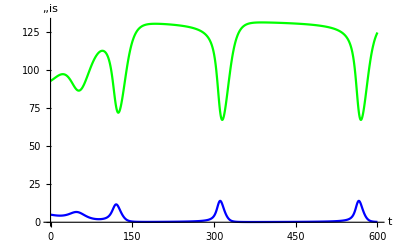

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

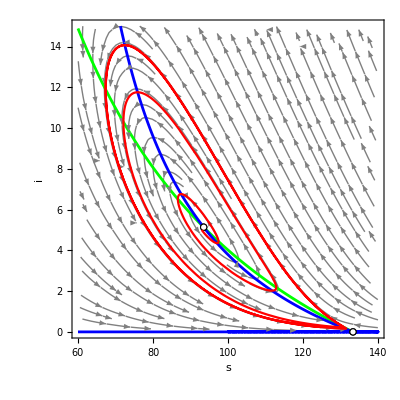

Final time slice is

254.473

The floquet exponents are

{-4.59451×10^-8,-0.0659782}

spB12E.pdf

solT12.pdf

```mathematica
ClearParameters;
T=600;
xM=140;
xm=60;
yM=15;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=25/4 //N
α=67/12//N

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB12E.pdf",sp]
Export["solT12.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions III and VI (between B1 and BT):

5.61538

5.01641

Fixed points:

{{s→133.333,i→0.},{s→84.1709,i→7.05842}}

Eigenvalues of FP:

{{-0.12,0},{0.0122452+0.131269 ⅈ,0.0122452-0.131269 ⅈ}}

Time plot around E2

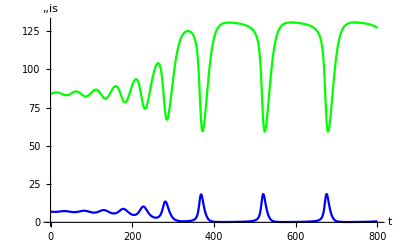

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

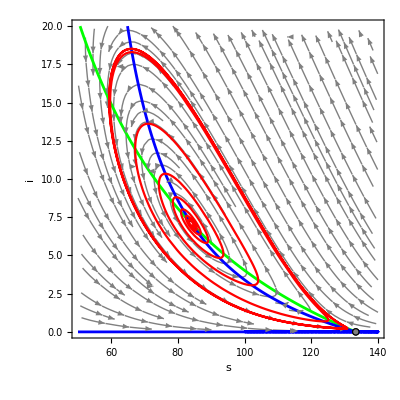

Final time slice is

155.023

The floquet exponents are

{2.50718×10^-8,-0.0534859}

spBP1E.pdf

solBP1.pdf

```mathematica
ClearParameters;
T=800;
xM=140;
xm=50;
yM=20;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=73/13//N
α=4891/975//N

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spBP1E.pdf",sp]
Export["solBP1.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions III and VI (another between B1 and BT):

6.09375

5.44375

Fixed points:

{{s→133.333,i→0.},{s→91.0252,i→5.60883}}

Eigenvalues of FP:

{{-0.12,0},{0.0210629+0.10705 ⅈ,0.0210629-0.10705 ⅈ}}

Time plot around E2

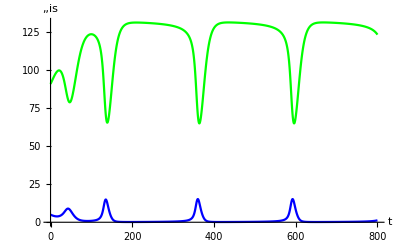

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

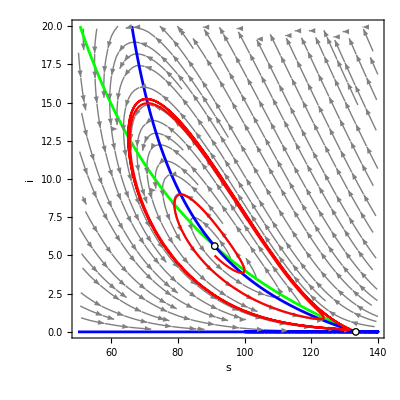

Final time slice is

231.915

The floquet exponents are

{8.82425×10^-10,-0.0647755}

spBP2E.pdf

solBP2.pdf

```mathematica
ClearParameters;
T=800;
xM=140;
xm=50;
yM=20;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=195/32(*11/2*)//N
α=871/160(*737/150*)//N

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spBP2E.pdf",sp]
Export["solBP2.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions III and VI ( between BT and B1 and closer to BT):

Fixed points:

{{s→133.333,i→0.},{s→92.4572,i→5.33361},{s→133.333,i→0.}}

Eigenvalues of FP:

{{-0.12,0},{0.022091+0.10223 ⅈ,0.022091-0.10223 ⅈ},{-0.12,0}}

Time plot around E2

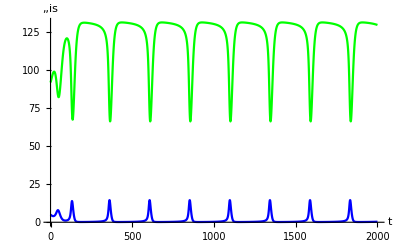

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

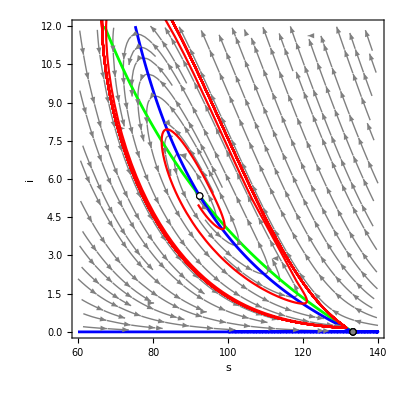

Final time slice is

245.34

The floquet exponents are

{3.41435×10^-8,-0.0656078}

```mathematica
ClearParameters;
T=2000;
xM=140;
xm=60;
yM=12;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;(*w=235/36;α=3149/540;*)
ω=18362/2969;α=1230254/222675;
Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
(*Export["spHPE.pdf",sp]
Export["solHP.pdf",psol]*)
```

#### Phase plot of the boundary R0=1 between Regions IV and II (Between B2 and BT):

7.16058

6.39679

Fixed points:

{{s→133.333,i→0.},{s→111.34,i→2.376}}

Eigenvalues of FP:

{{-0.12,0},{0.0103906+0.0502167 ⅈ,0.0103906-0.0502167 ⅈ}}

Time plot around E2

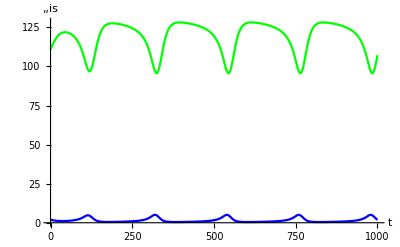

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

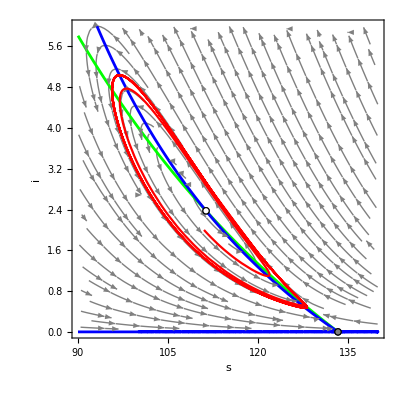

Final time slice is

219.938

The floquet exponents are

{-2.73386×10^-8,-0.0298991}

spB12bE.pdf

solT12b.pdf

```mathematica
ClearParameters;
T=1000;
xM=140;
xm=90;
yM=6;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=981/137//N
α=21909/3425//N

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB12bE.pdf",sp]
Export["solT12b.pdf",psol]
```

#### Phase plot of the boundary R0=1 (Between B2 and H):

7.91732

7.0728

Fixed points:

{{s→133.333,i→0.},{s→132.419,i→0.0828753},{s→133.333,i→0.}}

Eigenvalues of FP:

{{-0.12,0},{-0.111746,-0.0000342071},{-0.12,0}}

Time plot around E2

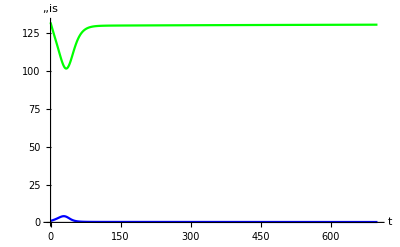

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

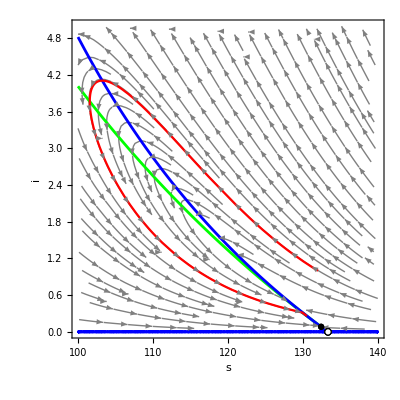

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spB2H.pdf

solB2H.pdf

```mathematica
ClearParameters;
T=700;
xM=140;
xm=100;
yM=5;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=8139/1028;α=181771/25700;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]+1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB2H.pdf",sp]
Export["solB2H.pdf",psol]
```

#### Phase plot of the boundary R0=1 (at BT):

Fixed points:

{{s→133.33333333333,i→0},{s→117.95130747349,i→1.5673723897566},{s→117.95130747349,i→1.5673723897566}}

Eigenvalues of FP:

{{-0.12,-0.013323676492},{0,0},{0,0}}

Time plot around E2

{s→118.051,i→1.59737}

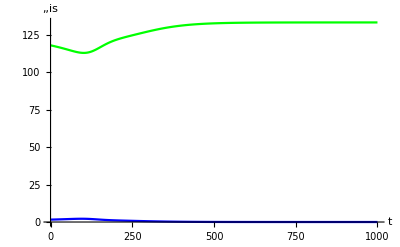

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

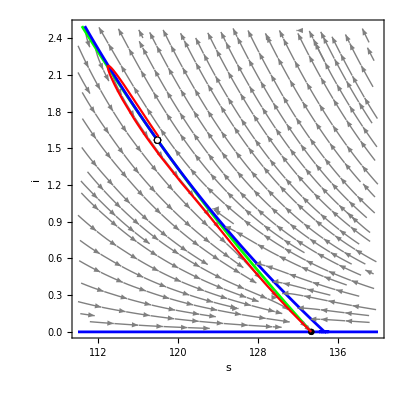

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spBTPE.pdf

solBTP.pdf

```mathematica
ClearParameters;
T=10^3;
xM=140;
xm=110;
yM=2.5;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3];
α=1/545531250(-1017750000+70750 Root[-837384000000000+7783000000 #1+293000 #1^2+#1^3&,3,0]+Root[-837384000000000+7783000000 #1+293000 #1^2+#1^3&,3,0]^2);

Print["Fixed points:"]
eq=N[equi,14](*Numeric fixed points*)

Print["Eigenvalues of FP:"]
eig=EcoEigenvalues[eq]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq//N,PlotMarkers->EcoStableQ[eq//N]]];
Print["Time plot around E2"]
E2n=RuleListTweak[eq[[2]],{s,i},{0.1,0.03}]
sol=EcoSim[E2n,T];
psol=PlotDynamics[sol,PlotPoints->200]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spBTPE.pdf",sp]
Export["solBTP.pdf",psol]
```

#### Phase plot of the boundary R0=1 (at B2):

7.35966

6.57463

Fixed points:

{{s→133.333,i→0.},{s→116.198,i→1.77275},{s→133.333,i→0.}}

Eigenvalues of FP:

{{-0.12,0},{0.+0.0391099 ⅈ,0.-0.0391099 ⅈ},{-0.12,0}}

Time plot around E2

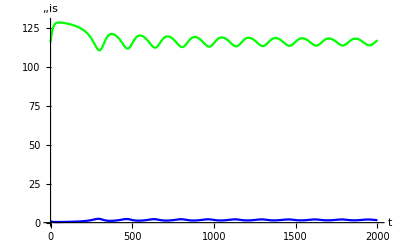

Finding the cycle using time slice

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

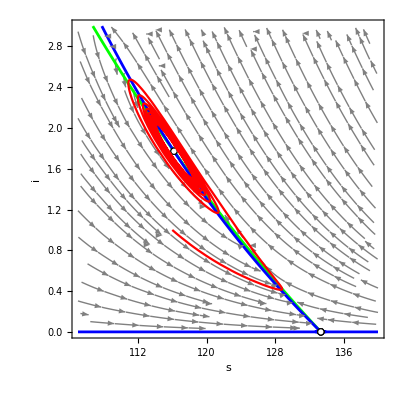

Final time slice is

160.805

The floquet exponents are

{-0.0000365264,-0.000058307}

spB2E.pdf

solB2.pdf

```mathematica
ClearParameters;
T=2000;
xM=140;
xm=105;
yM=3;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2,0];α=67/75 Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2,0];


Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB2E.pdf",sp]
Export["solB2.pdf",psol]
```

#### Phase plot of the boundary R0=1 (at B1):

5.15735

4.60724

Fixed points:

{{s→133.333,i→0.},{s→78.5251,i→8.44639},{s→133.333,i→0.}}

Eigenvalues of FP:

{{-0.12,0},{0.+0.152171 ⅈ,0.-0.152171 ⅈ},{-0.12,0}}

Time plot around E2

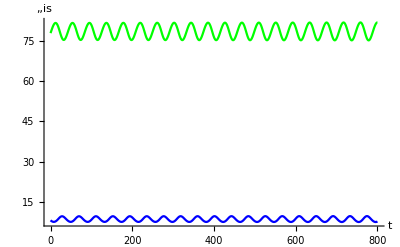

Finding the cycle using time slice

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

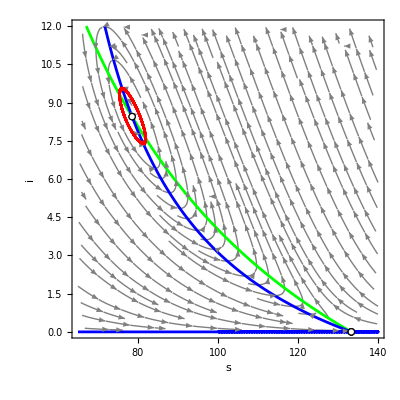

Final time slice is

42.2252

The floquet exponents are

{0.00181877,-0.000205883}

spBPE.pdf

solBP.pdf

```mathematica
ClearParameters;
T=800;
xM=140;
xm=65;
yM=12;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,1,0];
α=67/75 Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,1,0];

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->300],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spBPE.pdf",sp]
Export["solBP.pdf",psol]
```

#### Phase plot of the boundary R0=1 (at H):

TrE2=

-0.12

Fixed points:

{{s→133.333,i→0.},{s→133.333,i→0.},{s→133.333,i→0.}}

Eigenvalues of FP:

{{-0.12,0},{-0.12,0},{-0.12,0}}

Time plot around E2

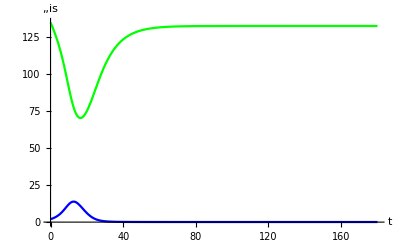

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

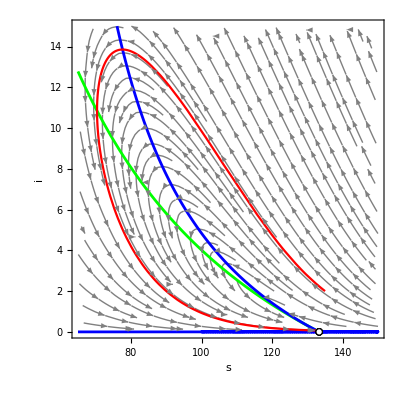

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spHPE.pdf

solHP.pdf

```mathematica
ClearParameters;
T=180;
xM=150;
xm=65;
yM=15;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=2010/253;
α=8978/1265;η=α/ω;
Print["TrE2="]
trE2//N
Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]]+2,i->IntegerPart[eq[[2,2]][[2]]]+2},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spHPE.pdf",sp]
Export["solHP.pdf",psol]
```

#### Phase plot of the boundary R0=1 (at B3):

Fixed points:

{{s→133.333,i→0.},{s→133.333,i→1.24666×10^-14}}

Eigenvalues of FP:

{{-0.12,0},{-0.12,0}}

Time plot around E2

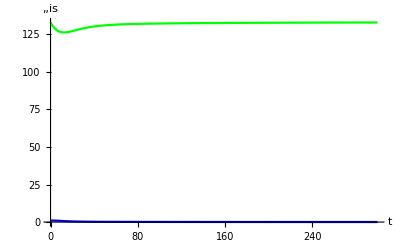

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

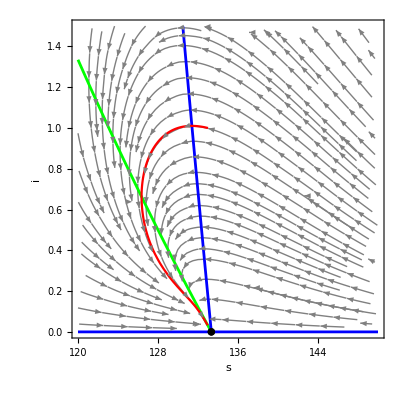

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spB3E.pdf

solB3.pdf

```mathematica
ClearParameters;
T=300;
xM=150;
xm=120;
yM=3/2;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;w=42.4504362201850;
α=37.9223896900319;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[2,1]][[2]]],i->IntegerPart[eq[[2,2]][[2]]]+1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB3E.pdf",sp]
Export["solB3.pdf",psol]
```

#### Phase plot of the boundary R0=1 between Regions II and IV (After HP):

Fixed points:

{{s→133.333,i→0.},{s→133.333,i→0.},{s→115.794,i→1.82095}}

Eigenvalues of FP:

{{-0.12,0},{-0.12,0},{0.000976665+0.0400896 ⅈ,0.000976665-0.0400896 ⅈ}}

Time plot around E2

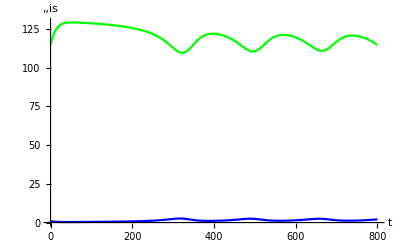

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

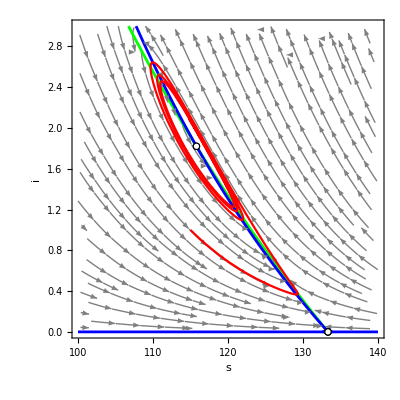

Final time slice is

163.987

The floquet exponents are

{-9.18309×10^-8,-0.00203132}

spB24E.pdf

solB24.pdf

```mathematica
ClearParameters;
T=800;
xM=140;
xm=100;
yM=3;
ym=0;

Λ=16 ;δ=2/10;γ=12/100;β=1/100;ξ=1/1000;μ=12/100;ω=235/32;
α=3149/480;


Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]]]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->IntegerPart[eq[[3,1]][[2]]],i->IntegerPart[eq[[3,2]][[2]]]},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spB24E.pdf",sp]
Export["solB24.pdf",psol]
```

# Gupta figures:

#### Phase plot of Fig 1 a) in Gupta:

Fixed points:

{{s→5.,i→0.},{s→3.35294,i→0.249912},{s→3.87623,i→0.146443}}

Eigenvalues of E2,E0,E1:

{{-0.3,-0.1},{0.012018+0.0764974 ⅈ,0.012018-0.0764974 ⅈ},{0.121831,-0.0411935}}

Time plot around DFE

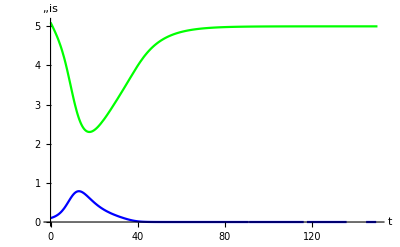

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

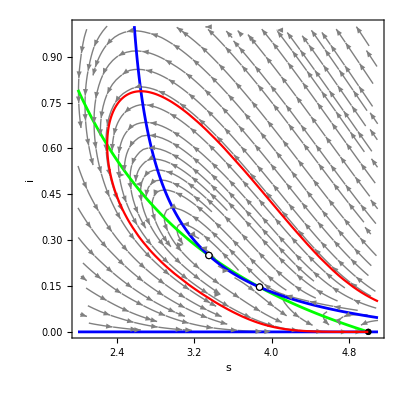

Final time slice is

453.519

The floquet exponents are

{-∞,-∞}

spGaE.pdf

solGa.pdf

```mathematica
ClearParameters;
T=150;
xM=5.1;
xm=2;
yM=1;
ym=0;
Λ=1/2 ;δ=1/5;γ=1/10;β=1/5;ξ=7/100;μ=1/10;

ω= 10/99;α=1/11;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of E2,E0,E1:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-9]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around DFE"]
sol=EcoSim[{s->5.1,i->0.1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spGaE.pdf",sp]
Export["solGa.pdf",psol]
```

#### Phase plot of Fig 1 b) in Gupta:

Fixed points:

{{s→5.,i→0.},{s→3.1916,i→0.289038},{s→4.03079,i→0.121247}}

Eigenvalues of E2,E0,E1:

{{-0.3,-0.1},{5.58554×10^-6+0.101011 ⅈ,5.58554×10^-6-0.101011 ⅈ},{0.144435,-0.0530554}}

Time plot around E2

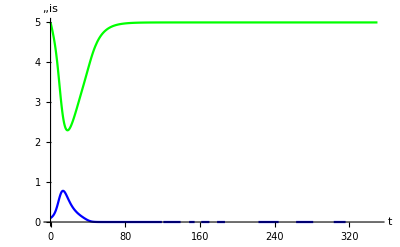

Finding the cycle using time slice

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

$Failed

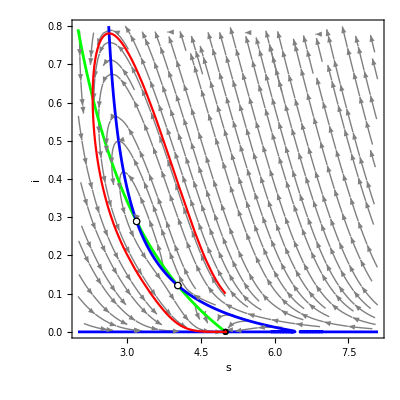

Final time slice is

FinalTime[$Failed]

The floquet exponents are

EcoEigenvalues[$Failed]

spGbE.pdf

solGb.pdf

```mathematica
T=350;
xM=8.1;
xm=2;
yM=.8;
Λ=1/2 ;δ=1/5;γ=1/10;β=1/5;ξ=7/100;μ=1/10;
ω=10000/103387;α=9000/103387;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of E2,E0,E1:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-12]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->5,i->0.1},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spGbE.pdf",sp]
Export["solGb.pdf",psol]
```

#### Phase plot of Fig 1 c) in Gupta:

Fixed points:

{{s→5.,i→0.},{s→3.08116,i→0.318321},{s→4.13484,i→0.105391}}

Eigenvalues of FP:

{{-0.3,-0.1},{-0.00915663+0.115223 ⅈ,-0.00915663-0.115223 ⅈ},{0.156612,-0.0594875}}

Time plot around DFE

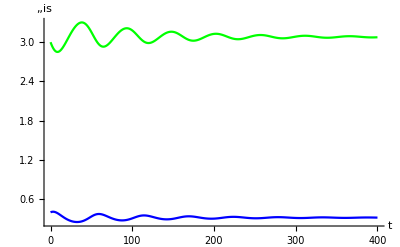

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

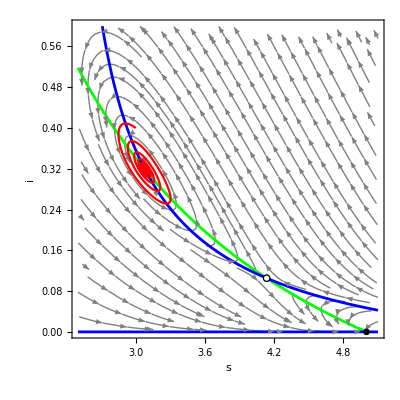

Final time slice is

1000.

The floquet exponents are

{-0.00915701+0.00212584 ⅈ,-0.00915701-0.00212584 ⅈ}

spGcE.pdf

solGc.pdf

Time plot around DFE

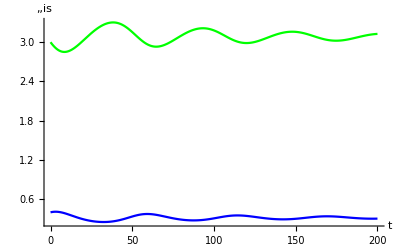

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

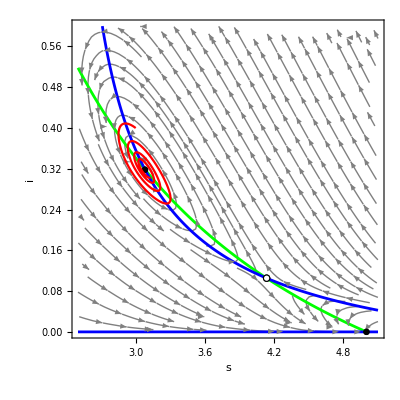

Final time slice is

19.1064

The floquet exponents are

{-0.00915663+0.115223 ⅈ,-0.00915663-0.115223 ⅈ}

spGcE.pdf

solGc.pdf

```mathematica
T=400;
xm=2.5;
yM=0.6;
Λ=1/2 ;δ=1/5;γ=1/10;β=1/5;ξ=7/100;μ=1/10;
ω=5/54;α=1/12;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-5]
pp=Shoω[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around DFE"]
sol=EcoSim[{s->3,i->0.4},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Shoω[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spGcE.pdf",sp]
Export["solGc.pdf",psol]
```

#### Phase plot of Fig 1 d) in Gupta:

Fixed points:

{{s→5.,i→0.},{s→3.04252,i→0.329097},{s→4.17091,i→0.100086}}

Eigenvalues of FP:

{{-0.3,-0.1},{-0.0125465+0.119857 ⅈ,-0.0125465-0.119857 ⅈ},{0.160369,-0.0615297}}

Time plot around E2

-Graphics-

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

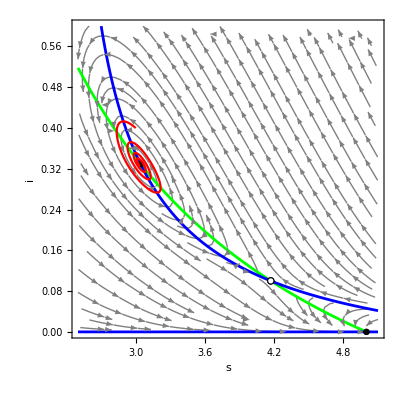

Final time slice is

19.1064

The floquet exponents are

{-0.00851491+0.114365 ⅈ,-0.00851491-0.114365 ⅈ}

spGdE.pdf

solGd.pdf

```mathematica
T=180;
xm=2.5;
yM=0.6;
ω=1/11;α=9/110;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of FP:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-5]
pp=Shoω[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->3,i->0.4},T];
psol
Print["Finding the cycle using time slice"]
lc
sp=Shoω[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spGdE.pdf",sp]
Export["solGd.pdf",psol]
```

#### Phase plot of Fig 3a) in Gupta:

Fixed points:

{{s→5.,i→0.},{s→3.11718,i→0.308529},{s→4.10105,i→0.110447}}

Eigenvalues of E2,E0,E1:

{{-0.3,-0.1},{-0.00608274+0.110756 ⅈ,-0.00608274-0.110756 ⅈ},{0.152885,-0.0574955}}

Time plot around E2

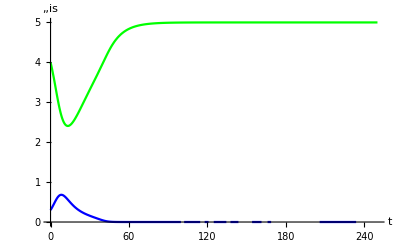

Finding the cycle using time slice

{i→InterpolatingFunction[…],s→InterpolatingFunction[…]}

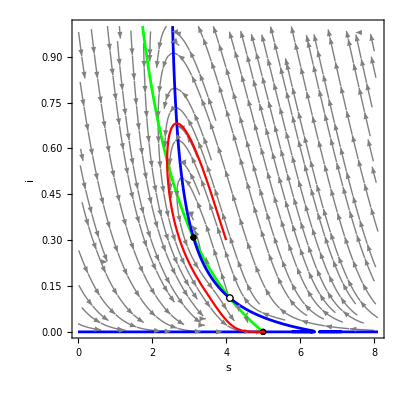

Final time slice is

648.762

The floquet exponents are

{-∞,-∞}

spG3aE.pdf

solG3a.pdf

```mathematica
T=250;
xM=8.1;
xm=0;
yM=1;

ω=100000000/1063265757;α=30000000/354421919;

Print["Fixed points:"]
eq=SelectValid[equi]//N
Print["Eigenvalues of E2,E0,E1:"]
Chop[Evaluate[EcoEigenvalues[eq]],10^-12]
pp=Show[PlotEcoPhasePlane[{s,xm,xM},{i,ym,yM},PlotPoints->200],RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]];
Print["Time plot around E2"]
sol=EcoSim[{s->4,i->0.3},T];
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
sp=Show[pp,RuleListPlot[sol,PlotStyle->Red]]
Print["Final time slice is"]
FinalTime[lc]
Print["The floquet exponents are"]
Chop[Evaluate[EcoEigenvalues[lc]]]
Export["spG3aE.pdf",sp]
Export["solG3a.pdf",psol]
```